# PHSX 591 Solar Flares & CMEs

## Problem Set 1 Roy Smart Due Feb. 15th

```mathematica
Clear["Global`*"]
```

## Problem 1

### Part a.

#### The flux function for Figure 1a is given by

```mathematica
Ap = λ ArcTan[(y+b)/z]-λ ArcTan[(y+a)/z]+λ ArcTan[(y-a)/z]-λ ArcTan[(y-b)/z];
```

#### Define the assumptions for this expression

```mathematica
$Assumptions = λ ∈ Reals && a > 0 && b>0
```

λ∈Reals&&a>0&&b>0

#### Plot this function to see what it looks like

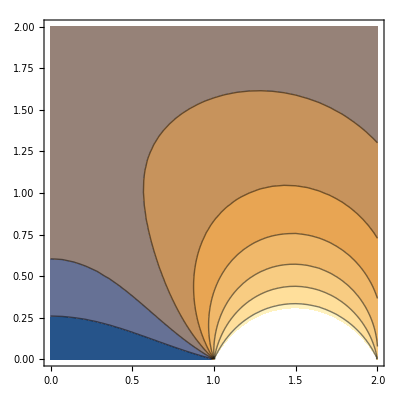

```mathematica
ContourPlot[Ap /. {b-> 2, a-> 1, λ->1},{y,0,2},{z,0,2}]
```

#### The X point is located where the magnetic field is equal to zero. Therefore, we will begin by taking a derivative of the flux function to determine the magnetic field.

```mathematica
Bp = Cross[Grad[Ap,{x,y,z}],{1,0,0}] //FullSimplify
```

{0,((a (1/(1+(a-y)^2/z^2)+1/(1+(a+y)^2/z^2))+y (-1/(1+(a-y)^2/z^2)+1/(1+(b-y)^2/z^2)+1/(1+(a+y)^2/z^2)-1/(1+(b+y)^2/z^2))-b/(1+(b-y)^2/z^2)-b/(1+(b+y)^2/z^2)) λ)/z^2,((-1/(1+(a-y)^2/z^2)+1/(1+(b-y)^2/z^2)+1/(1+(a+y)^2/z^2)-1/(1+(b+y)^2/z^2)) λ)/z}

#### Evaluate this field at y=0

```mathematica
Bpz = Bp /. y -> 0
```

{0,(((2 a)/(1+a^2/z^2)-(2 b)/(1+b^2/z^2)) λ)/z^2,0}

#### Find the height for which all components of the magnetic field are zero by solving the y-component for z

```mathematica
sol1aa=Solve[Bpz[[2]] == 0, z] //FullSimplify
```

{{z→-√(a b)},{z→√(a b)}}

#### Select the positive solution, since we are interested in the height of the X point above the photosphere

```mathematica
zx = sol1aa[[2,1,2]]
```

√(a b)

#### The flux between this X point and the origin is given by evaluating the flux function at this X point.

```mathematica
ψp12 = Ap /. {y-> 0,z-> zx} //FullSimplify
```

2 λ (-ArcTan[√(a/b)]+ArcTan[√(b/a)])

#### Check limit by expanding about a/b=0

```mathematica
Series[ψp12 /. b-> 1,{a,0,1}]/. a -> 0
```

π λ

#### Check another limit by expanding about a/b=1

```mathematica
Series[ψp12 /. b-> 1,{a,1,1}] /.a-> 1 //Quiet
```

0

### Part b.

#### The change in flux can be written as

```mathematica
Δψp12 = (ψp12 /. a -> a+ Δa ) - ψp12 //FullSimplify
```

2 λ (ArcTan[√(a/b)]-ArcTan[√(b/a)]+ArcTan[√(b/(a+Δa))]-ArcTan[√((a+Δa)/b)])

#### Write b in terms of a

```mathematica
b=2a;
```

#### Expand the change in flux about Δa/a=0 to leading order.

```mathematica
Normal[Series[Δψp12/. a-> 1,{Δa,0,1}]]
```

-2/3 √2 Δa λ